## Hayes & Adams (2017) Mathematica Notebook 4 Monte Carlos & Model Projections for the MYTH Model

This document is a pdf created from a Wolfram Mathematica notebook prepared by Mark A. Hayes during December 2016, following the general approach for logistic regression and Monte Carlo simulations outlined in Hayes (2011). This code and output supports the analysis described in Hayes, M. A. and R. A. Adams. 2017. Simulated bat populations collapse when exposed to conditions that mimic climate change projections for western North America. PLOS ONE. If you would like a copy of the original Mathematica notebook, please contact MAH at hayesm@usgs.gov or hayes.a.mark@gmail.com.  

This uses the model Temp + Precip with beta estimates from the full model. 

Mark A. Hayes
January 10, 2017

### Set the directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

\\IGSKBACBFS2\groups\bts\t\mah\manuscripts\2016\Hayes & Adams 2016 - Bat pop modeling - PLOS ONE\revision - fall winter 2016\Plos One - Data package

#### Deterministic repro rate = 0.85

```mathematica
DetRepro = {0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85};
```

## RCP 2.6 Projections and Simulations

### Model projections using RCP26 2009-2086 average values

Predicted probability of an adult female being reproductively active in a given year, given RCP26 average values for years 2009-2086, using logistic regressiion.

```mathematica
ProbRCP26Ave = {0.854439036,0.853162005,0.852679695,0.85523147,0.85649353,0.85649353,0.860224818,0.861450399,0.860224818,0.858523827,0.859761893,0.860990877,0.862210818,0.863421751,0.862210818,0.862210818,0.86581674,0.869342596,0.868176144,0.86581674,0.86581674,0.867000872,0.865369437,0.866556907,0.866111689,0.863721136,0.86083478,0.858365415,0.85960464,0.85711707,0.85711707,0.858365415,0.858365415,0.861294735,0.862055871,0.863721136,0.861294735,0.85711707,0.85960464,0.862512434,0.864920875,0.866556907,0.866556907,0.86581674,0.863421751,0.86581674,0.864623713,0.867443585,0.864623713,0.868615539,0.866262788,0.866262788,0.862666951,0.858523827,0.856020316,0.857276647,0.857276647,0.857276647,0.857746418,0.857746418,0.85523147,0.85523147,0.853480063,0.853480063,0.854754799,0.852196074,0.850414369,0.851711142,0.854754799,0.851711142,0.852998617,0.851711142,0.854276827,0.858056198,0.862210818,0.860990877,0.859761893,0.862210818};
Mean[ProbRCP26Ave]
```

0.860147

```mathematica
ProbRCP26Min ={0.849933053,0.849116734,0.84730456,0.849933053,0.848128929,0.846806464,0.853006907,0.860538013,0.851233269,0.847633039,0.849442008,0.855078186,0.85806425,0.86099879,0.859769864,0.864631451,0.871225859,0.873078613,0.873078613,0.869638457,0.867301226,0.870360699,0.86759341,0.867151121,0.865521243,0.863121813,0.858523827,0.855545804,0.855545804,0.849600205,0.855545804,0.858056198,0.857746418,0.856020316,0.854754799,0.858523827,0.856020316,0.850902799,0.857746418,0.860686462,0.858214899,0.859455225,0.865225196,0.865672904,0.864928599,0.864928599,0.863728917,0.869638457,0.864928599,0.865672904,0.863728917,0.858840208,0.855867726,0.854601096,0.8523602,0.85106811,0.844467299,0.838496395,0.836233512,0.835357108,0.825823358,0.824346887,0.829651306,0.822670488,0.812953653,0.813537582,0.809822378,0.810413802,0.817196591,0.815663315,0.815663315,0.809430711,0.811980677,0.818148621,0.824714536,0.82526964,0.831631356,0.842782441};
Mean[ProbRCP26Min]
```

0.848975

```mathematica
ProbRCP26Max ={0.855384619,0.846628691,0.848773911,0.845627559,0.850082399,0.85267139,0.861900777,0.860216868,0.860678535,0.859447239,0.868756702,0.863567618,0.869918786,0.868317708,0.871072108,0.87377727,0.874901302,0.875321499,0.871503279,0.868026878,0.86640609,0.865217486,0.867585815,0.871503279,0.871072108,0.86640609,0.862357772,0.861138923,0.863567618,0.864019967,0.862813496,0.862357772,0.861138923,0.864019967,0.867143504,0.867143504,0.863567618,0.860678535,0.859447239,0.863866733,0.867877469,0.868317708,0.870639706,0.872644609,0.869194452,0.876433724,0.876433724,0.870786457,0.866111689,0.874622913,0.875740486,0.877949993,0.872361931,0.866111689,0.868466695,0.873071287,0.871933219,0.872361931,0.872361931,0.869194452,0.867293617,0.868026878,0.869194452,0.869194452,0.871933219,0.867293617,0.863267949,0.870353239,0.875321499,0.871933219,0.865217486,0.865960447,0.869483096,0.879987985,0.878903332,0.878903332,0.878222023,0.884635966};
Mean[ProbRCP26Max]
```

0.86751

```mathematica
aReproRCP26Ave =ProbRCP26Ave;
```

```mathematica
aReproRCP26Min =ProbRCP26Min;
```

```mathematica
aReproRCP26Max =ProbRCP26Max;
```

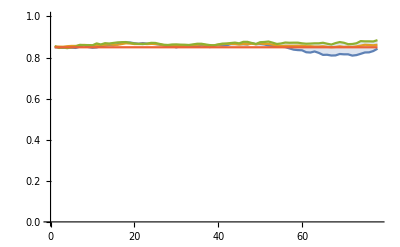

```mathematica
ListLinePlot[{aReproRCP26Min,aReproRCP26Ave,aReproRCP26Max, DetRepro},PlotRange->{0,1},Filling->{1->{3}},PlotRange->{{0,77},{0.5,1}}]
```

### Monte Carlo RCP 26 simulation

```mathematica
SAave=0.79;
SAmin=SAave*0.90;
SAmax=SAave*1.10;

SFave=SAave*0.64;
SFmin=SFave*0.90;
SFmax=SFave*1.10;

aReproAve=SAave*(aReproRCP26Ave/2);
aReproMin=aReproAve*0.90;
aReproMax=aReproAve*1.10;

jReproAve=0.90*(aReproRCP26Ave/2)*SFave;
jReproMin=jReproAve*0.90;
jReproMax=jReproAve*1.10;

runs=10000;
j=0;
```

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax},SFave]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin[[i]],jReproMax[[i]]},jReproAve[[i]]]]))+(Nne*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Nthree*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

2582.97

519.457

1248.

5376.

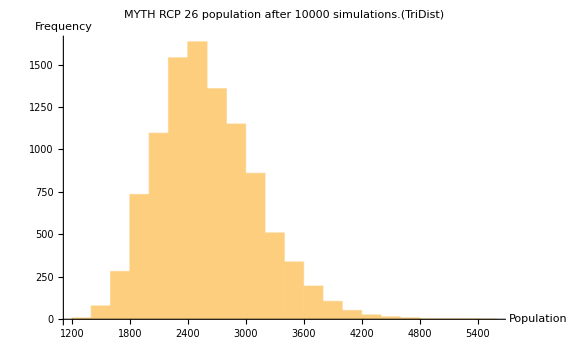

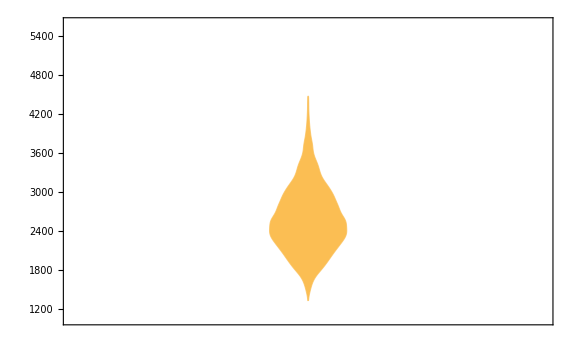

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,PlotLabel->StringJoin["MYTH RCP 26 population after ",ToString[runs]," simulations.","(TriDist)"],AxesLabel->{"Population","Frequency"}]
DistributionChart[Round[MonteCarlo]]
```

## RCP 4.5 Projections and Simulations

### Model projections using RCP45 2009-2086 average values

Predicted probability of an adult female being reproductively active in a given year, given RCP45 average values for years 2009-2086, using logistic regression.

```mathematica
ProbRCP45Ave = {0.869638457,0.865672904,0.869201969,0.868034452,0.866413742,0.865225196,0.864776228,0.864326,0.86788505,0.86788505,0.86788505,0.865073108,0.862666951,0.858523827,0.856805583,0.856805583,0.855545804,0.855069993,0.858832193,0.858832193,0.85711707,0.858365415,0.855859571,0.85105973,0.846628691,0.847952415,0.846128791,0.844792096,0.840209602,0.842937588,0.842427897,0.842427897,0.843781188,0.844621091,0.84595899,0.84276492,0.840890753,0.842254773,0.838998514,0.837088131,0.83568815,0.836563137,0.839341473,0.847943891,0.849258285,0.849258285,0.849258285,0.847943891,0.849258285,0.847943891,0.843437208,0.838822343,0.841569547,0.842928835,0.841569547,0.845618928,0.845116339,0.843772473,0.842419121,0.845618928,0.842419121,0.841056253,0.843772473,0.839165606,0.836384821,0.833031412,0.834449545,0.835858006,0.837256821,0.837256821,0.838646017,0.841908062,0.838646017,0.838646017,0.837256821,0.837256821,0.835858006,0.838646017};
Mean[ProbRCP45Ave]
```

0.848054

```mathematica
ProbRCP45Min ={0.859926962,0.862373466,0.862373466,0.855715003,0.860694389,0.853006907,0.851719492,0.855078186,0.858373452,0.854601096,0.858373452,0.855392797,0.850256877,0.837629749,0.84227234,0.845474581,0.847633039,0.848455953,0.851875713,0.845806281,0.841248104,0.843626719,0.84530419,0.845636189,0.833583837,0.829282508,0.837797987,0.825260107,0.824704979,0.833402918,0.831083045,0.836750328,0.840899598,0.840384545,0.841239274,0.835697228,0.837966085,0.836045845,0.832686879,0.82432774,0.82432774,0.822280153,0.828181719,0.831073764,0.834458677,0.840550472,0.843781188,0.837265829,0.836393868,0.834989098,0.838654963,0.83250518,0.830533312,0.834809403,0.833926891,0.838998514,0.836215404,0.835338922,0.833040607,0.839174529,0.833040607,0.834107355,0.830716715,0.824883809,0.82432774,0.825804338,0.820213905,0.82616958,0.826534217,0.823580952,0.818128947,0.82115366,0.825616731,0.82115366,0.822651197,0.822651197,0.819646249,0.816601737};
Mean[ProbRCP45Min]
```

0.837147

```mathematica
ProbRCP45Max ={0.88476894,0.880125591,0.884376378,0.882267608,0.882267608,0.883721787,0.88266638,0.876849499,0.87904201,0.87971936,0.877537415,0.870353239,0.869918786,0.868905267,0.871933219,0.874901302,0.872216707,0.871072108,0.873352622,0.869771198,0.870058758,0.871211023,0.868168578,0.864463306,0.864463306,0.8640122,0.86280567,0.857419911,0.85314544,0.854900166,0.856164629,0.852663084,0.852179419,0.851694441,0.856477277,0.850886023,0.853463527,0.847775733,0.845116339,0.844612414,0.842419121,0.844612414,0.855053606,0.863705571,0.864905426,0.862797844,0.864004431,0.859588681,0.865649839,0.866390784,0.858658023,0.853137156,0.850554917,0.850554917,0.851529705,0.851529705,0.85409799,0.848430449,0.848924206,0.850231623,0.852335239,0.851042968,0.854414367,0.849249822,0.845278253,0.849249822,0.849249822,0.850554917,0.852335239,0.842583329,0.849249822,0.847438958,0.838813404,0.836901252,0.836901252,0.833556321,0.835848935,0.838116103};
Mean[ProbRCP45Max]
```

0.85894

```mathematica
aReproRCP45Ave =ProbRCP45Ave;
```

```mathematica
aReproRCP45Min =ProbRCP45Min;
```

```mathematica
aReproRCP45Max =ProbRCP45Max;
```

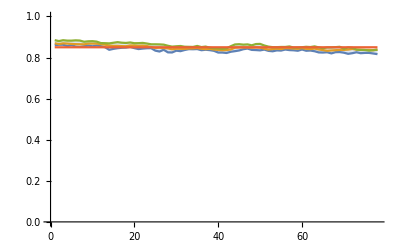

```mathematica
ListLinePlot[{aReproRCP45Min,aReproRCP45Ave,aReproRCP45Max, DetRepro},PlotRange->{0,1},Filling->{1->{3}}]
```

### Monte Carlo RCP 45 simulation

```mathematica
SAave=0.79;
SAmin=SAave*0.90;
SAmax=SAave*1.10;

SFave=SAave*0.64;
SFmin=SFave*0.90;
SFmax=SFave*1.10;

aReproAve=SAave*(aReproRCP45Ave/2);
aReproMin=aReproAve*0.90;
aReproMax=aReproAve*1.10;

jReproAve=0.90*(aReproRCP45Ave/2)*SFave;
jReproMin=jReproAve*0.90;
jReproMax=jReproAve*1.10;

runs=10000;
j=0;
```

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax},SFave]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin[[i]],jReproMax[[i]]},jReproAve[[i]]]]))+(Nne*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Nthree*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

2001.68

408.445

783.

4392.

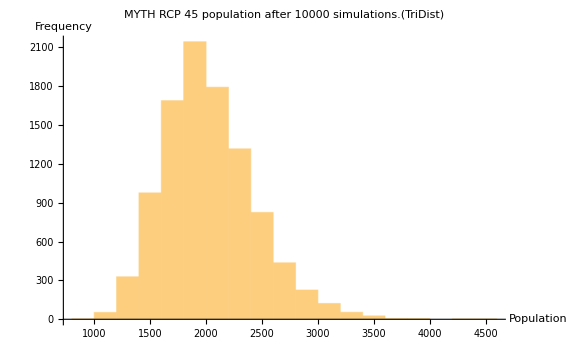

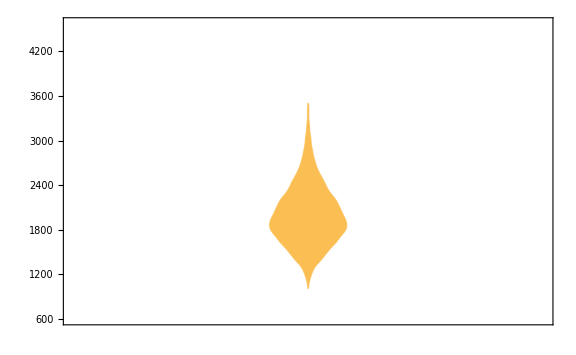

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,PlotLabel->StringJoin["MYTH RCP 45 population after ",ToString[runs]," simulations.","(TriDist)"],AxesLabel->{"Population","Frequency"}]
DistributionChart[Round[MonteCarlo]]
```

## RCP 6.0

### Model projections using RCP60 2009-2086 average values

Predicted probability of an adult female being reproductively active in a given year, given RCP60 average values for years 2009-2086, using logistic regression:
Average RCP60 values for years 2009-2086 (from 1995, substract 15):

```mathematica
ProbRCP60Ave = {0.868912797,0.870073707,0.870073707,0.866119356,0.863728917,0.863275753,0.867301226,0.865672904,0.865672904,0.864027735,0.865225196,0.866413742,0.86759341,0.86759341,0.86596812,0.867151121,0.86788505,0.86788505,0.863874508,0.862666951,0.863874508,0.862666951,0.863421751,0.86581674,0.861753413,0.860067999,0.855859571,0.855859571,0.855859571,0.853316968,0.851546421,0.85105973,0.848447452,0.847952415,0.847952415,0.844792096,0.842937588,0.841578362,0.839692741,0.837789003,0.836393868,0.834458677,0.831073764,0.831073764,0.835338922,0.838134042,0.840890753,0.837611765,0.837088131,0.838478488,0.836563137,0.837957108,0.836563137,0.836036783,0.834098206,0.835509067,0.832141311,0.833565493,0.834449545,0.835858006,0.835329828,0.833917735,0.837256821,0.836732265,0.836732265,0.83195914,0.829982157,0.826524738,0.829438929,0.827438446,0.82597278,0.82245127,0.821889145,0.821889145,0.819819347,0.819819347,0.822822035,0.824308591};
Mean[ProbRCP60Ave]
```

0.846114

```mathematica
ProbRCP60Min ={0.856661805,0.86038943,0.854924767,0.852368519,0.856189052,0.859926962,0.863583196,0.859926962,0.861154733,0.858222944,0.86099879,0.857754485,0.856501656,0.856501656,0.856028464,0.855553974,0.854285057,0.857125167,0.857125167,0.860075956,0.862520274,0.860075956,0.863728917,0.861302633,0.850256877,0.843118847,0.837975061,0.840733965,0.840393413,0.837629749,0.832877622,0.834647802,0.836054908,0.832696089,0.831804562,0.831265973,0.836928323,0.830726012,0.833583837,0.829282508,0.824337314,0.81623078,0.817186714,0.823221057,0.825072038,0.830542617,0.829097872,0.828552403,0.824516439,0.821536239,0.814297304,0.810203262,0.804835463,0.80643743,0.815839377,0.817371516,0.806833781,0.810983548,0.812546804,0.818700322,0.82115366,0.830533312,0.825062496,0.829448282,0.823949863,0.823949863,0.823391463,0.815829443,0.81926051,0.821707917,0.813507493,0.81716696,0.813507493,0.804015095,0.80622353,0.803006889,0.810383327,0.811950395};
Mean[ProbRCP60Min]
```

0.834042

```mathematica
ProbRCP60Max ={0.880667704,0.88026306,0.879180552,0.872507014,0.872507014,0.868615539,0.873215681,0.875043912,0.875043912,0.873920977,0.870500267,0.871218441,0.873496742,0.871933219,0.86640609,0.871072108,0.871072108,0.875598557,0.874901302,0.868756702,0.871503279,0.870639706,0.87249966,0.872071342,0.868168578,0.864615974,0.860522143,0.856325091,0.854584666,0.854106229,0.85234356,0.846620106,0.842081495,0.843437208,0.847943891,0.843944239,0.846620106,0.848765425,0.842419121,0.845116339,0.84002562,0.844107153,0.844107153,0.841395658,0.846780733,0.853781044,0.851529705,0.852818483,0.852335239,0.848430449,0.841734474,0.842583329,0.841221614,0.848756939,0.842410344,0.845107685,0.837771033,0.837247812,0.838116103,0.837247812,0.833556321,0.836375774,0.837771033,0.837771033,0.838292897,0.84053275,0.837771033,0.840016735,0.843591829,0.83949937,0.829069767,0.824676304,0.822631905,0.83141168,0.827977307,0.827977307,0.83087209,0.835669993};
Mean[ProbRCP45Max]
```

0.85894

```mathematica
aReproRCP60Ave =ProbRCP60Ave;
```

```mathematica
aReproRCP60Min =ProbRCP60Min;
```

```mathematica
aReproRCP60Max =ProbRCP60Max;
```

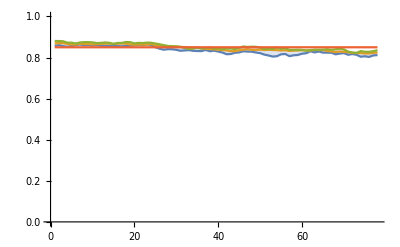

```mathematica
ListLinePlot[{aReproRCP60Min,aReproRCP60Ave,aReproRCP60Max, DetRepro},PlotRange->{0,1},Filling->{1->{3}}]
```

### Monte Carlo RCP 60 simulation

```mathematica
SAave=0.79;
SAmin=SAave*0.90;
SAmax=SAave*1.10;

SFave=SAave*0.64;
SFmin=SFave*0.90;
SFmax=SFave*1.10;

aReproAve=SAave*(aReproRCP60Ave/2);
aReproMin=aReproAve*0.90;
aReproMax=aReproAve*1.10;

jReproAve=0.90*(aReproRCP60Ave/2)*SFave;
jReproMin=jReproAve*0.90;
jReproMax=jReproAve*1.10;

runs=10000;
j=0;
```

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax},SFave]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin[[i]],jReproMax[[i]]},jReproAve[[i]]]]))+(Nne*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Nthree*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

1931.48

390.902

898.

4175.

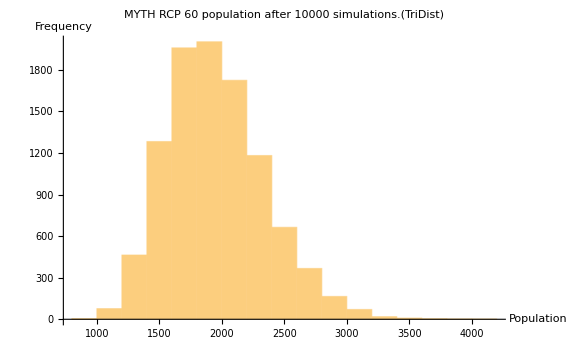

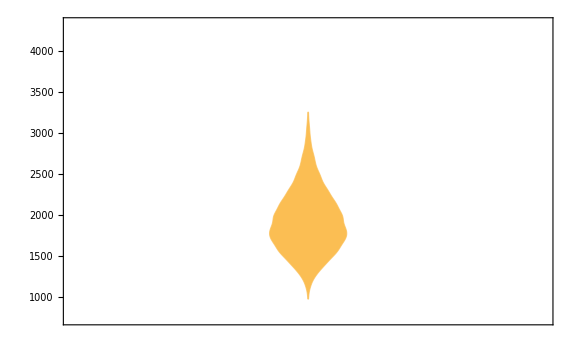

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,PlotLabel->StringJoin["MYTH RCP 60 population after ",ToString[runs]," simulations.","(TriDist)"],AxesLabel->{"Population","Frequency"}]
DistributionChart[Round[MonteCarlo]]
```

## RCP 8.5

### Model projections using RCP85 2009-2086 average values

Predicted probability of an adult female being reproductively active in a given year, given RCP85 average values for years 2009-2086, using logistic regression:
Average RCP85 values for years 2009-2086 (from 1995, substract 15):

```mathematica
ProbRCP85Ave = {0.861605918,0.857436075,0.859918998,0.860686462,0.860686462,0.860224818,0.865073108,0.863421751,0.860530078,0.860530078,0.860067999,0.860067999,0.854592881,0.854114467,0.856645568,0.85617277,0.853153723,0.851381548,0.848773911,0.845627559,0.841065091,0.841916861,0.840550472,0.837265829,0.835338922,0.834809403,0.828543011,0.828543011,0.826534217,0.827447885,0.828903701,0.825428964,0.824874259,0.830707417,0.827261678,0.828172311,0.829623273,0.827624502,0.830524007,0.829982157,0.83088138,0.830340439,0.831238152,0.827800976,0.825785316,0.824308591,0.823751086,0.824676304,0.822631905,0.820568855,0.821507158,0.820942694,0.818864321,0.813685144,0.810953143,0.809379715,0.802377027,0.801766665,0.795595742,0.795595742,0.794969787,0.792666078,0.786932729,0.781084622,0.782174591,0.779766944,0.7755645,0.769495764,0.765156354,0.765156354,0.756308873,0.746030159,0.742619909,0.741884356,0.739920433,0.737202665,0.734466688,0.733716189};
Mean[ProbRCP85Ave]
```

0.818636

```mathematica
ProbRCP85Min ={0.858690114,0.856189052,0.851398278,0.855239655,0.851719492,0.849933053,0.852524175,0.856341358,0.848623494,0.845474581,0.845474581,0.846307038,0.843118847,0.847633039,0.843961653,0.840218478,0.83970164,0.84192566,0.842436672,0.838663908,0.826179075,0.828191126,0.830542617,0.822660843,0.816035159,0.812358241,0.809219337,0.803830448,0.796051615,0.800989287,0.805836573,0.795426697,0.800375704,0.808423249,0.809410314,0.8150646,0.810393486,0.805029771,0.801186478,0.793329758,0.796664402,0.792698672,0.795415938,0.797486436,0.79416179,0.79520372,0.793948607,0.794991337,0.796653692,0.788665095,0.789727481,0.79310509,0.788447736,0.781541399,0.776697028,0.763336897,0.766325579,0.765636394,0.762405566,0.76792034,0.774462541,0.775576007,0.768824858,0.76700154,0.771764958,0.771764958,0.763783726,0.755611776,0.744583058,0.751095535,0.735976473,0.728451169,0.723616597,0.726927442,0.718729186,0.722076092,0.716391583,0.724631869};
Mean[ProbRCP85Min]
```

0.798569

```mathematica
ProbRCP85Max ={0.875598557,0.871787579,0.875179161,0.877810237,0.874479892,0.870639706,0.874758553,0.875875087,0.870925634,0.870925634,0.872782077,0.87235457,0.866549262,0.87235457,0.875314284,0.874894066,0.87063226,0.866247468,0.855529462,0.849907754,0.852015127,0.850231623,0.847607422,0.850231623,0.847110136,0.844774758,0.834970878,0.835499981,0.832132076,0.837247812,0.842747398,0.835320734,0.83949937,0.842237205,0.841725667,0.837070098,0.837070098,0.83846058,0.840357939,0.843083865,0.84257456,0.837939153,0.844766089,0.841551917,0.839666042,0.838804465,0.836018657,0.835490894,0.833547148,0.823741487,0.825221968,0.825588174,0.822060557,0.815417478,0.822431961,0.820367093,0.816757315,0.820741261,0.821678858,0.817137326,0.810352848,0.80758354,0.792237261,0.793286396,0.79495901,0.795997941,0.790332357,0.775110347,0.772647314,0.776888668,0.775552992,0.767664347,0.775995017,0.781284855,0.781718769,0.777542943,0.769703471,0.767652556};
Mean[ProbRCP85Max]
```

0.832461

```mathematica
aReproRCP85Ave =ProbRCP85Ave;
```

```mathematica
aReproRCP85Min =ProbRCP85Min;
```

```mathematica
aReproRCP85Max =ProbRCP85Max;
```

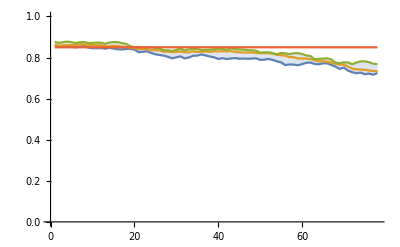

```mathematica
ListLinePlot[{aReproRCP85Min,aReproRCP85Ave,aReproRCP85Max, DetRepro},PlotRange->{0,1},Filling->{1->{3}}]
```

### Monte Carlo RCP 85 simulation

```mathematica
SAave=0.79;
SAmin=SAave*0.90;
SAmax=SAave*1.10;

SFave=SAave*0.64;
SFmin=SFave*0.90;
SFmax=SFave*1.10;

aReproAve=SAave*(aReproRCP85Ave/2);
aReproMin=aReproAve*0.90;
aReproMax=aReproAve*1.10;

jReproAve=0.90*(aReproRCP85Ave/2)*SFave;
jReproMin=jReproAve*0.90;
jReproMax=jReproAve*1.10;

runs=10000;
j=0;
```

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax},SFave]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin[[i]],jReproMax[[i]]},jReproAve[[i]]]]))+(Nne*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Nthree*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

1106.75

231.282

530.

2422.

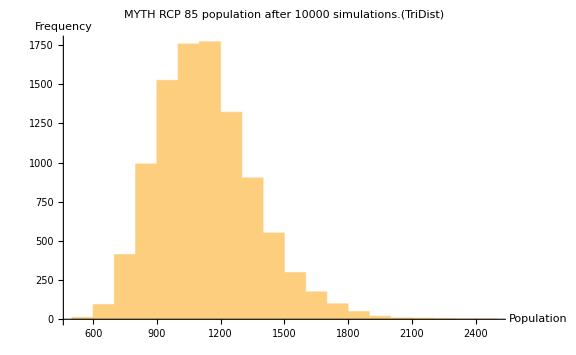

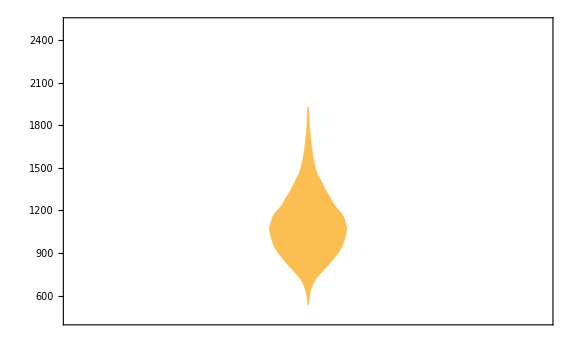

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,PlotLabel->StringJoin["MYTH RCP 85 population after ",ToString[runs]," simulations.","(TriDist)"],AxesLabel->{"Population","Frequency"}]
DistributionChart[Round[MonteCarlo]]
```